## Equilibration Time

The standard Newtonian equilibration time estimate suggests the disk reaches steady state only inside r~6 M.  Equilibration time versus r:

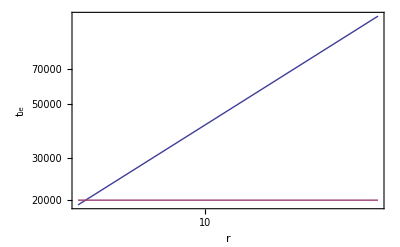

```mathematica
tie[r_]:=1300 r^(3/2)
LogLogPlot[{tie[r],20000},{r,6,20},
Frame->True,
FrameLabel->{"r","t_ie"},
LabelStyle->18]
```

Useful functions for writing GR corrections :

```mathematica
x[r_]:=Sqrt[r]

Z1[a_]:=1+(1-a^2)^(1/3)((1+a)^(1/3)+(1-a)^(1/3))
Z2[a_]:=(3 a^2+Z1[a]^2)^(1/2)

rms[a_]:=(3+Z2[a]-Sign[a]((3-Z1[a])(3+Z1[a]+2Z2[a]))^(1/2))
x0[a_]:=rms[a]^(1/2)
x1[a_]:=2 Cos[1/3 ArcCos[a]-π/3]
x2[a_]:=2 Cos[1/3 ArcCos[a]+π/3]
x3[a_]:=-2 Cos[1/3 ArcCos[a]]

AA[a_,r_]:=1+a^2/r^2+2 a^2/r^3
BB[a_,r_]:=1+a/r^(3/2)
CC[a_,r_]:=1-3/r+2a/r^(3/2)
DD[a_,r_]:=1-2/r+a^2/r^2
EE[a_,r_]:=1+4 a^2/r^2-4 a^2/r^3+3 a^4/r^4
FF[a_,r_]:=1-2a/r^(3/2)+a^2/r^2
LL[a_,r_]:=FF[a,r]/CC[a,r]^(1/2)-LISCO[a]/r^(1/2)
(* a=0 (Page and Thorne): *)
QQa0[a_,r_]:=1/x[r] 1/((1-3 x[r]^-2)^(1/2))(x[r]-x0[a]-3/2 a Log[x[r]/x0[a]]-(3(x1[a]-a)^2)/(x1[a](x1[a]-x2[a])(x1[a]-x3[a]))Log[(x[r]-x1[a])/(x0[a]-x1[a])]-(3(x3[a]-a)^2)/(x3[a](x3[a]-x1[a])(x3[a]-x2[a]))Log[(x[r]-x3[a])/(x0[a]-x3[a])])

(* a!=0 (Page and Thorne): *)
QQ[a_,r_]:=1/x[r](1+a x[r]^-3)/((1-3 x[r]^-2+2a x[r]^-3)^(1/2))(x[r]-x0[a]-3/2 a Log[x[r]/x0[a]]-(3(x1[a]-a)^2)/(x1[a](x1[a]-x2[a])(x1[a]-x3[a]))Log[(x[r]-x1[a])/(x0[a]-x1[a])]-(3(x2[a]-a)^2)/(x2[a](x2[a]-x1[a])(x2[a]-x3[a]))Log[(x[r]-x2[a])/(x0[a]-x2[a])]-(3(x3[a]-a)^2)/(x3[a](x3[a]-x1[a])(x3[a]-x2[a]))Log[(x[r]-x3[a])/(x0[a]-x3[a])])
```

The calculations of NT include corrections from GR (cf. their equations 5.9.6, 5.9.8, and 5.9.10 ).  The Newtonian equilibration time is multiplied by a correction factor which goes to 1 as r -> ∞.  The correction factors are different in the inner, middle, and outer regions of the disk.  But in the inner and middle regions of the disk they are similar and in both cases the equilibration time at r = 12 is reduced by a factor of about 0.3.

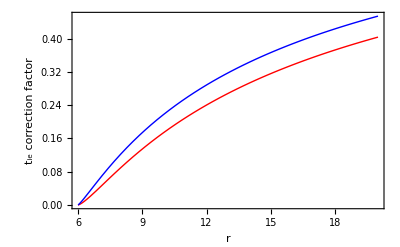

```mathematica
(* Correction factors: *)
GRfixInnera0[a_,r_]:=AA[a,r]^(1/10)BB[a,r]^(-4/5)CC[a,r]^(1/2)DD[a,r]^(-7/20)EE[a,r]^(-1/20)QQa0[a,r]^(7/10)
GRfixMiddlea0[a_,r_]:=BB[a,r]^(-4/5)CC[a,r]^(1/2)DD[a,r]^(-3/10)QQa0[a,r]^(3/5)
GRfixOutera0[a_,r_]:=AA[a,r]^-2 BB[a,r]^3 CC[a,r]^(1/2)DD[a,r]^(1/2)EE[a,r] QQa0[a,r]^-1

(* As a function of r (a=0): *)
Plot[{GRfixInnera0[0,r],GRfixMiddlea0[0,r]},{r,6,20},
Frame->True,
PlotStyle->{Red,Blue},
FrameLabel->{"r","t_ie correction factor"},
LabelStyle->18]
```

The new viscous time estimate, with correction factors appropriate to the "inner" or "middle" disk regions, suggests the disk is converged out to r~13 M.

NT equilibration time versus r for the inner and middle disk regions (a=0):

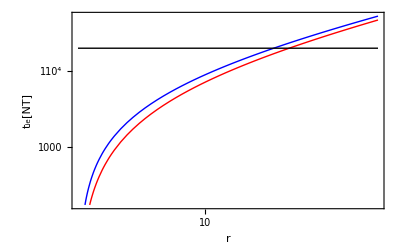

```mathematica
tieInnera0[a_,r_]:=tie[r]GRfixInnera0[a,r]
tieMiddlea0[a_,r_]:=tie[r]GRfixMiddlea0[a,r]
LogLogPlot[{tieInnera0[0,r],tieMiddlea0[0,r],20000},{r,6,20},
Frame->True,
PlotStyle->{Red,Blue,Black},
FrameLabel->{"r","t_ie[NT]"},
LabelStyle->18]
```

```mathematica
tieMiddlea0[0,13.]
```

19374.8

The correction factors increase with black hole spin, so that the a>0 disks take longer to equilibrate.  

At r=12M, the correction factors versus spin a:

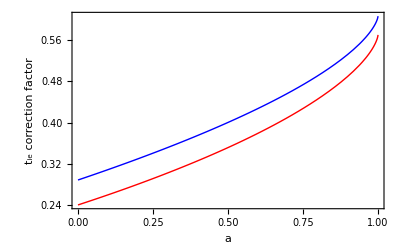

```mathematica
(* Correction factors: *)
GRfixInner[a_,r_]:=AA[a,r]^(1/10)BB[a,r]^(-4/5)CC[a,r]^(1/2)DD[a,r]^(-7/20)EE[a,r]^(-1/20)QQ[a,r]^(7/10)
GRfixMiddle[a_,r_]:=BB[a,r]^(-4/5)CC[a,r]^(1/2)DD[a,r]^(-3/10)QQ[a,r]^(3/5)
GRfixOuter[a_,r_]:=AA[a,r]^-2 BB[a,r]^3 CC[a,r]^(1/2)DD[a,r]^(1/2)EE[a,r] QQ[a,r]^-1
(* As a function of r (a=0): *)
Plot[{GRfixInner[a,12],GRfixMiddle[a,12]},{a,0.001,1},
Frame->True,
PlotStyle->{Red,Blue},
FrameLabel->{"a","t_ie correction factor"},
LabelStyle->18]
```

Equilibration time versus r, for our fiducial spins:

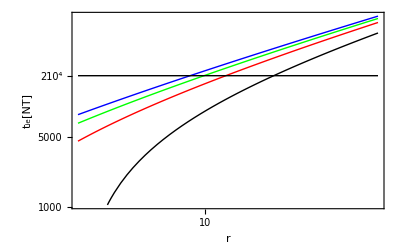

```mathematica
tieInner[a_,r_]:=tie[r]GRfixInner[a,r]
tieMiddle[a_,r_]:=tie[r]GRfixMiddle[a,r]
LogLogPlot[{
tieMiddlea0[0,r],
tieMiddle[0.7,r],
tieMiddle[0.9,r],
tieMiddle[0.98,r],
20000},{r,6,20},
Frame->True,
PlotStyle->{Black,Red,Green,Blue,Black},
FrameLabel->{"r","t_ie[NT]"},
LabelStyle->18]
```

We see that with h/r, \alpha, and the simulation time kept fixed, the higher spin models equilibrate over a smaller range of radii.